# More Eigen Stuff

I am going to avoid mesh transfers and/or matrix transfers by staying in Mathematica today!

## Homogenous Dirichlet Boundary Conditions Everywhere!

## Our Rectangle

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,9];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456789

## A Square

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,6];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,16];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

12345678910111213141516

## Options

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,6,
Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.005}}}}];
TabView[
Table[i->ContourPlot[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## Homogenous Neumann Boundary Conditions Everywhere!

## Our Rectangle: Neumann Conditions

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,6];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## A Square

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,6];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,12];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456789101112

## Homogenous Neumann Boundary Conditions Not Everywhere!

## Our Rectangle: Mixed Dirichlet/Neumann Conditions

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,x>2], DirichletCondition[u[x,y]==0.,x≤2]},
u,{x,y}∈Omega,6];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,
PlotRange->All,
PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,x>0.5], DirichletCondition[u[x,y]==0.,x≤0.5]},
u,{x,y}∈Omega,12];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456789101112

# Eigen Stuff: What is it good for!

## Heat Equation

Suppose I want to solve the heat equation u_t=Δu on some domain omega with some reasonable set of boundary conditions.  Then I immediately know a few things:

There are a complete countable set of eigenfunctions u_i  for -Δ (incorporating the boundary conditions) with matching non-negative eigenvalues λ_i

Every solution of the heat equation is a (possibly officially infinite) weighted sum of terms e^-λ_it u_i

If the eigenvalues are ordered 0≤λ_1≤λ_2≤… then in practice the solution is well approximated after a short time by the sum of the first few product solutions a_1 e^-λ_1t u_1+a_2 e^-λ_2t u_2+…+a_s e^-λ_st u_s

The key to this is that the “higher” exponentials decay VERY rapidly.

## Vibrations

Suppose I want to solve the wave equation u_tt=Δu on some domain omega with some reasonable set of boundary conditions.  Then I immediately know a few things:

There are a complete countable set of eigenfunctions u_i  for -Δ (incorporating the boundary conditions)  with matching non-negative eigenvalues λ_i

Every solution of the wave equation is a (possibly officially infinite) weighted sum of terms sin(√λ_i t)u_i and cos(√λ_i t)u_i

The wave equation is different because these terms do not decay!

# Back To Eigen Stuff

Laplacian eigenfunctions have a pretty amazing and incredibly useful property!

## Homogenous Dirichlet Boundary Conditions Everywhere!

## Our Rectangle

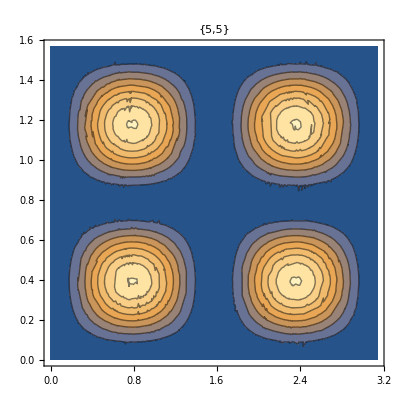

1.

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,6];
{i,j}={5,5};
ContourPlot[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
NIntegrate[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
AccuracyGoal->5]
```

## A Square

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,6];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

-Graphics3D-

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,12];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

-Graphics3D-

## Options

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}],DirichletCondition[u[x,y]==0,True]},
u,{x,y}∈Omega,6,
Method->{"PDEDiscretization"->{"FiniteElement",{"MeshOptions"->{"MaxCellMeasure"->0.5}}}}];
TabView[
Table[i->Plot3D[EFuns⟦i⟧[x,y],{x,y}∈Omega,PlotLabel->StringForm["λ=``",EVals⟦i⟧]],{i, Length[EVals]}]
]
```

123456

## Homogenous Neumann Boundary Conditions Everywhere!

## Our Rectangle: Neumann Conditions

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,6];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

-Graphics3D-

## A Square

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,6];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

123456

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,True]},
u,{x,y}∈Omega,12];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

-Graphics3D-

## Homogenous Neumann Boundary Conditions Everywhere!

## Our Rectangle: Mixed Dirichlet/Neumann Conditions

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Rectangle[{0,0},{π,π/2}];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,x>2], DirichletCondition[u[x,y]==0.,x≤2]},
u,{x,y}∈Omega,6];
{i,j}={2,3};
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
```

-Graphics3D-

## A Disk

```mathematica
Clear[Omega,EVals,EFuns,u];
Omega=Disk[{0,0},1];
{EVals,EFuns}=NDEigensystem[
{-Laplacian[u[x,y],{x,y}]+NeumannValue[0,x>0.5], DirichletCondition[u[x,y]==0.,x≤0.5]},
u,{x,y}∈Omega,12];
Plot3D[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
PlotLabel->{i,j}]
NIntegrate[EFuns⟦i⟧[x,y]*EFuns⟦j⟧[x,y],{x,y}∈ Omega,
AccuracyGoal->4]
```

-Graphics3D-

4.61183×10^-7